# M712 Applied Math in Mechanics

Prof. Douglas P. Holmes
Mechanical Engineering
Boston University

## Introduction to Mathematica

Arithmetic

Numerical Calculation: Input arithmetic, press SHIFT+ENTER to evaluate:

```mathematica
27.7+19.94
```

47.64

You can use either a space or * for multiplication (the x shows up automatically when multiplying numbers), i.e.

```mathematica
18.4 12.1
18.4*12.1
```

222.64

222.64

You can use either a / or CTRL+/ for division, i.e.

```mathematica
1/3 +1/3
```

2/3

You get an exact result from Mathematica unless you request otherwise (in this case, // N or N[ ]):

```mathematica
1/3 +1/3 //N
```

0.666667

Functions and Syntax

Mathematical functions (and, all functions in Mathematica) begin with a capital letter and are followed by square brackets:

```mathematica
Sin[π/2]
```

1

```mathematica
Sqrt[2]
```

√2

```mathematica
Random[](*between 0 and 1*)
```

0.514892

```mathematica
N[Pi,30]
```

3.14159265358979323846264338328

You can suppress output with a ;

```mathematica
Sin[π/2];
```

Clear a variable or function with

```mathematica
Clear[v]
v
```

v

```mathematica
Clear[f]
f[x]
```

f[x]

You can write special characters by typing, e.g. ESC alpha ESC

```mathematica
α;
```

Define a function with the following syntax, note the _ following the variable and the := (delayed assign)

```mathematica
f[x_]:=x^2+3x-5
```

```mathematica
f[3]
```

13

List all variables and functions defined across all open MMA notebooks

```mathematica
Names["Global`*"]
```

{f,v,x,x$,α}

Clear all variables and functions defined across all open MMA notebooks (even better: Evaluation/Quit Kernel/Local)

```mathematica
ClearAll["Global`*"]
```

Lists, Matrices, Vectors, and Tensors

A vector (or a tensor) is a List, denoted by curly brackets

```mathematica
v={1.1,0.7,0.1}
```

{1.1,0.7,0.1}

Raising a variable, vector, or number to a power is done by ^ or CMD+6

```mathematica
v^2
```

```mathematica
{1.2100000000000002,0.48999999999999994,0.010000000000000002}
```

{1.21,0.49,0.01}

Call the second element of the list (vector) v:

```mathematica
v[[2]]
```

0.7

```mathematica
t ={{a,b},{b,a}}
```

```mathematica
{{a,b},{b,a}}
```

{{a,b},{b,a}}

The % symbol means “last output”, be VERY careful with using this...

```mathematica
%//MatrixForm
```

(a | b
b | a)

Calculus

Differentiate a function using D[function, variable] or with ‘

```mathematica
f[x_] =-4 + 3x + x^2
D[f[x],x]
```

-4+3 x+x^2

3+2 x

```mathematica
f'[x]
```

3+2 x

```mathematica
D[D[f[x],x],x]
```

2

```mathematica
f''[x]
```

2

Indefinite integration of a function using Integrate[function, variable]

```mathematica
Integrate[f[x],x]
```

-4 x+(3 x^2)/2+x^3/3

Definite integration of a function using Integrate[function, {variable, min, max}]

```mathematica
Integrate[f[x],{x,0,1}]
```

-13/6

Solving Equations

Define an equation using a double equal sign

```mathematica
Solve[f[x]==7,x]
```

{{x→1/2 (-3-√53)},{x→1/2 (-3+√53)}}

```mathematica
3 x^2==a
```

3 x^2==a

Solve equations using Solve[ ]

```mathematica
Solve[3 x^2 == a,x]
```

{{x→-(√a)/(√3)},{x→(√a)/(√3)}}

Solve a system of equations by...

```mathematica
Solve[{x+2y==5, 7x-5y==-3}, {x,y}]
```

{{x→1,y→2}}

Equations that cannot be solved algebraically can be solved numerically, for instancing by root finding

```mathematica
FindRoot[Cos[x]==x, {x,0}]
```

{x→0.739085}

Solve a differential equation with boundary conditions. To Mathematica, this is treated as a system of equations.

```mathematica
eq=ϵ y''[x]+2y'[x]+2y[x]==0;
bc1=y[0]==0;
bc2= y[1]==1;
```

```mathematica
aSol=y[x]/.DSolve[{eq,bc1,bc2},y[x],x][[1]][[1]]
```

-(ⅇ^(1/ϵ+(√(1-2 ϵ))/ϵ) (ⅇ^(x (-1/ϵ-(√(1-2 ϵ))/ϵ))-ⅇ^(x (-1/ϵ+(√(1-2 ϵ))/ϵ))))/(-1+ⅇ^((2 √(1-2 ϵ))/ϵ))

Numerically solve a differential equation with initial conditions. Since this is solved numerically, we need to choose a value of ϵ. The output from Mathematica is not very useful so let’s plot the solution (we’ll talk about plotting in the next section).

```mathematica
eqN=x''[t]==-1/(1+ϵ x[t])^2;
ic1N=x[0]==0;
ic2N=x'[0]==1;
```

```mathematica
s=NDSolve[{eqN/.ϵ->0.1, ic1N,ic2N}, x,{t,0,3}];
```

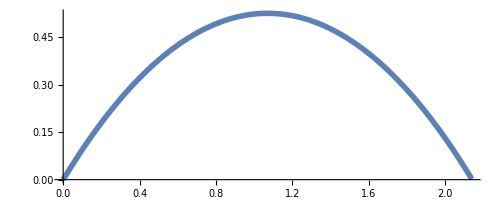

```mathematica
numPlot=Plot[Evaluate[x[t]/.s],{t,0,2.14},PlotStyle->Thickness[0.01],AspectRatio->Automatic]
```

Plotting

### Basic Plotting

Basic plotting of a single function

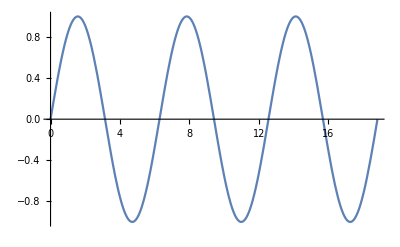

```mathematica
Plot[Sin[x],{x,0,6 Pi}]
```

Basic plotting of multiple functions

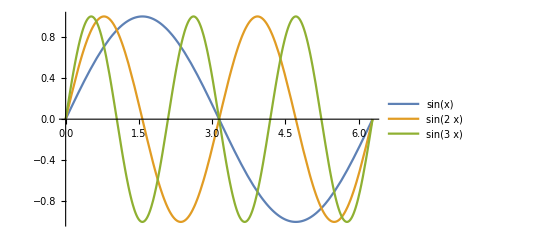

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```

Filling a plot beneath a curve

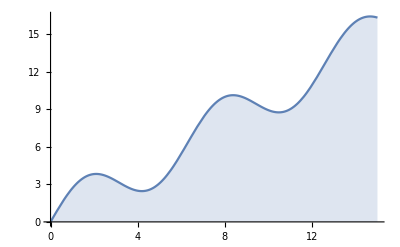

```mathematica
Plot[2 Sin[x]+x,{x,0,15},Filling->Bottom]
```

Filling between two plots

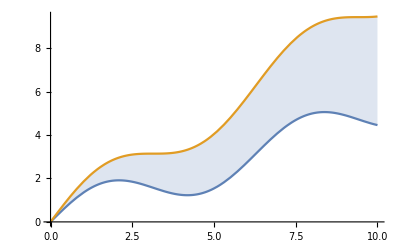

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x},{x,0,10},Filling->{1->{2}}]
```

Log-Log plots. One can also explore LogLinearPlot[ ] and LogPlot[ ] ...

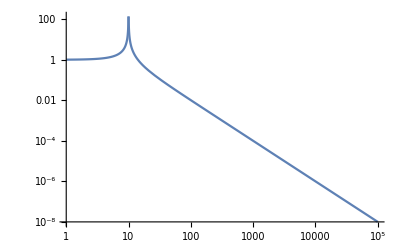

```mathematica
LogLogPlot[Abs[10^2/((I ω)^2+100)],{ω,10^0,10^5}]
```

Plot a function in 3D

```mathematica
Plot3D[(x^2+y^2) Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

### Plotting Data

Data is inputted as a list data={{x1, y1}, {x2,y2},...}

```mathematica
data={
{1,1.2},
{2,2.4},
{3,3.1},
{4,4.7},
{5,5.2},
{6,6.8},
{7,7.8},
{8,8.3},
{9,9.7}
};
```

Plot the data using a list plot

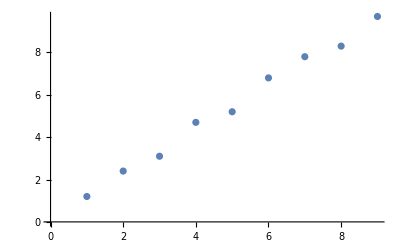

```mathematica
ListPlot[data]
```

Plots can be stored as variables too, this will be useful in a moment...

```mathematica
dataPlot=ListPlot[data];
```

Let’s fit our data using a linear regression, and plot it

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[0.2+1.05333 x]

```mathematica
Normal[model]
```

0.2+1.05333 x

```mathematica
modelPlot=Plot[model[x],{x,0,10}];
```

Now we can combine our data and model in one graph

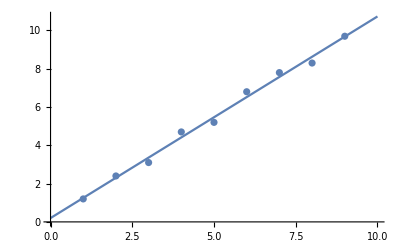

```mathematica
Show[modelPlot,dataPlot]
```

Let’s improve the presentation of our graph

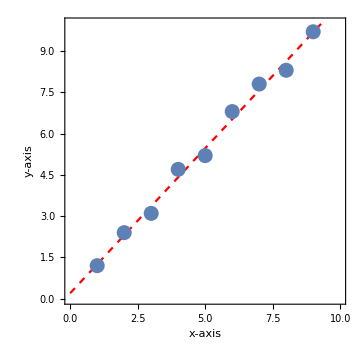

```mathematica
modelPlotNice=Plot[model[x],{x,0,10},
PlotRange->{{0,10},{0,10}}, 
PlotStyle->{Red,Dashed}, 
AspectRatio->1, 
Frame->True,
FrameLabel->{"x-axis","y-axis"},
ImageSize->Medium,
BaseStyle->{FontSize->16}
];
dataPlotNice=ListPlot[data, 
PlotStyle->Directive[PointSize[0.03]]
];
Show[modelPlotNice,dataPlotNice]
```

### Advanced Plotting

Before we get into advanced plotting, it’s important to know how Mathematica generates lists, similar to For loops in other languages. Mathematica uses Table[ ]

```mathematica
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Simply replace the word Table with the word Manipulate, and you get an interactive application that lets you explore values of n with a slider.

```mathematica
Manipulate[n,{n,1,20}]
```

Add “Labeled” to see the value of the variable

```mathematica
Manipulate[n,{n,1,20, Appearance->"Labeled"}]
```

Now lets use this to Manipulate a graph

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}]
```

You have as many control parameters as you want, and you have discrete options that might affect the presentation of the graph

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{Axis,Top,Bottom}}]
```